# The temperature-size rule is predicted to stabilize consumer-resource dynamics under warming

## UBC MST group

Made with Mathematica 9

## Preliminaries

Plot settings

```mathematica
LabelSize=35; (*size of axis label text*)
FigureSize=650;  (*size of figure*)
TickSize=20;  (*size of tick text*)
Pad={{90,25},{70,10}};  (*whitespace to leave around figures, {{left,right},{bottom,top}}*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.1,0.5};  (*relative location of y axis label position*)
LetterSize=20;  (*size of text in stability plots*)
```

Directories

```mathematica
SetDirectory[NotebookDirectory[]]; (*set current directory to be location of this file*)
imagedir="";(*directory to save figures in*)
```

## The underlying consumer-resource dynamics (and re-creating Gilbert et al. Figure 3)

Equations 1 and 2 from Gilbert et al 2014 (with potential temperature dependencies added)

```mathematica
dRdt[R_,C_,T_]:=r[T] R(1-R/K[T])-f[R,T] R C;
dCdt[R_,C_,T_]:=e[T] f[R,T]R C-m[C,T]C;
```

where R is biomass of resource, C is biomass of consumer, T is temperature, K is resource carrying capacity, f is the functional response, e is the conversion efficiency of resources into new consumers, and m is consumer mortality.

BCR at a given T, as defined by Gilbert (Eqn 5),

```mathematica
BCR[T_]:=(e[T] a[T]K[T])/m[T]
```

Equilibrium biomasses at given temperature assuming a type I functional response and density-independent consumer mortality (as in most of Gilbert)

```mathematica
Eq[T_]:=Solve[{0==dRdt[R,C,T],0==dCdt[R,C,T]}/.f[R,T]->a[T]/.m[C,T]->m[T],{R,C}]
```

Equilibrium consumer to resource biomass ratio at a given temperature (at the equilibrium where both populations persist)

```mathematica
CR[T_]:=C/R/.Eq[T][[3]]
```

The Jacobian evaluated at equilibrium (linear stability analysis)

```mathematica
Jac={{D[dRdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],R],D[dRdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],C]},{D[dCdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],R],D[dCdt[R,C,T]/.f[R,T]->a[T]/.m[C,T]->m[T],C]}}/.Eq[T][[3]];
```

The eigenvalues of the Jacobian are

```mathematica
lambda=Eigenvalues[Jac];
```

Using equation for K in Table 1 of Gilbert. Want K = 100 at 15C (as in Figure 3 of Gilbert), so we need rate-constant K0 to be

```mathematica
K15=Solve[100==K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T/.T->273.15+15,K0];
```

Reproducing Figure 3A of Gilbert (same shape but numbers too large; can’t tell why from their figure legend)

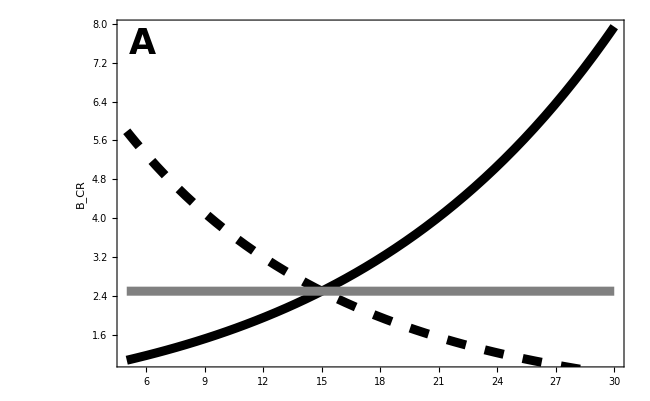

```mathematica
Show[
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Black,Thickness[0.01]}],
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.32,{T,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]}],
Plot[BCR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.9/.ES->0.9,{T,5,30},PlotStyle->{Gray,Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

Export[imagedir<>"BCRGilbert.eps",%];
```

Figure 3b of Gilbert (off by factor of ~3)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

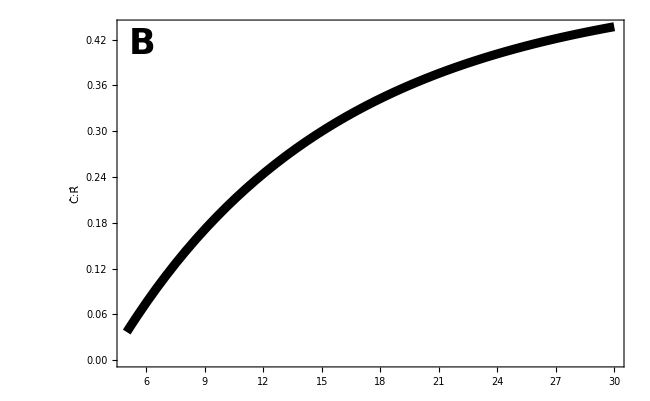

```mathematica
Show[Plot[ CR[T]/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9,{T,5,30},PlotStyle->{Black,Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
]

Export[imagedir<>"CtoRGilbert.eps",%];
```

Figure 3c of Gilbert (pretty close)

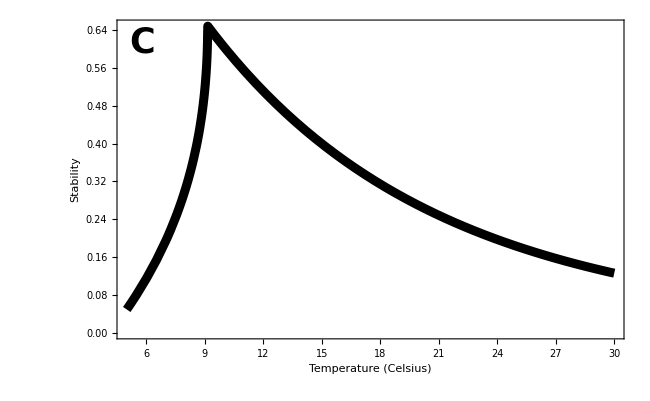

```mathematica
Show[Plot[-Max[Re[lambda/.K[T]->K0 Exp[EB/(k T[R])-ES/(k T[S])]/.T[i_]->T+273.15/.K15/.k->8.62*10^-5/.a[T]->0.1/.e[T]->0.15/.m[T]->0.6/.r[T]->2/.EB->0.32/.ES->0.9]],{T,5,30},PlotStyle->{Black,Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos]
}
]

Export[imagedir<>"StabilityGilbert.eps",%];
```

## Adding temperature dependence

Here we add all the temperature dependencies, according to Table 1 of Gilbert et al.

```mathematica
cr={C,R};
GilbertTable1={
r[T]->r[M] Exp[-EB/(k T[R])],
K[T]->K[M] Exp[EB/(k T[R])-ES/(k T[S])],
m[T]->m[M] Exp[-Em/(k T[C])],
a[T]->a[M] Sqrt[Sum[(ν0[cr[[i]]] Exp[-Eν[cr[[i]]]/(k T[cr[[i]]])])^2,{i,1,Length[cr]}]],
e[T]->e[M]
};
```

To have the same population dynamics parameter values at 15 degrees as we did above with temperature dependence only in K, we need

```mathematica
aM15=Solve[0.1==a[T]/.GilbertTable1/.T[i_]->273.15+15,a[M]]//Flatten
```

{a[M]→0.1/(√(ⅇ^(-(0.00694083 Eν[C])/k) ν0[C]^2+ⅇ^(-(0.00694083 Eν[R])/k) ν0[R]^2))}

```mathematica
eM15=Solve[0.15==e[T]/.GilbertTable1/.T[i_]->273.15+15,e[M]]//Flatten
```

{e[M]→0.15}

```mathematica
KM15=Solve[100==K[T]/.GilbertTable1/.T[i_]->273.15+15,K[M]]//Flatten
```

{K[M]→100. ⅇ^(-(0.00347041 EB)/k+(0.00347041 ES)/k)}

```mathematica
rM15=Solve[2==r[T]/.GilbertTable1/.T[i_]->273.15+15,r[M]]//Flatten
```

{r[M]→2. ⅇ^((0.00347041 EB)/k)}

```mathematica
mM15=Solve[0.6==m[T]/.GilbertTable1/.T[i_]->273.15+15,m[M]]//Flatten
```

{m[M]→0.6 ⅇ^((0.00347041 Em)/k)}

Now, BCR as a function of temperature is

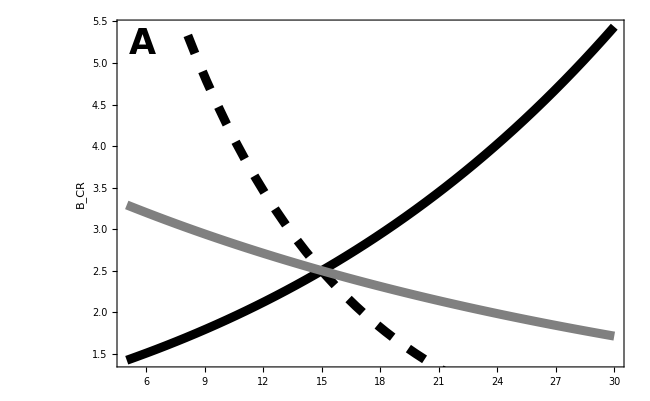

```mathematica
Show[
Plot[BCR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
Plot[BCR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Gray}],
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

Export[imagedir<>"BCRAllTempDep.eps",%];
```

This is the same qualitative result as Gilbert et al Figure 3A, with the gray curve now with a slightly non-zero slope (because, although K doesn’t vary with T, other parameters now do).

The biomass ratio is

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

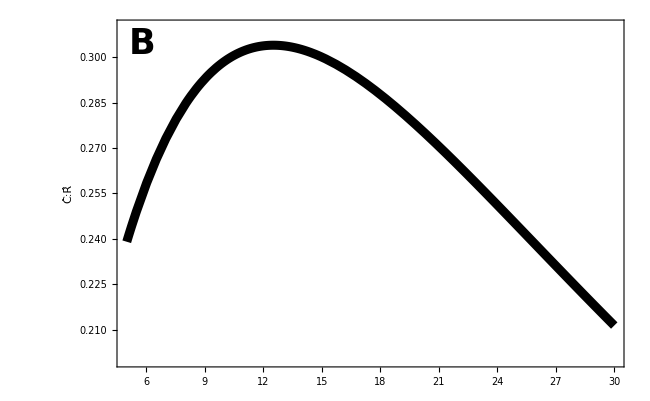

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
PlotRange->{{5,30},{0.2,0.31}},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
]

Export[imagedir<>"CtoRAllTempDep.eps",%];
```

The ratio now decreases at high temperatures (as opposed to the increase in Gilbert et al Figure 3B).

And stability:

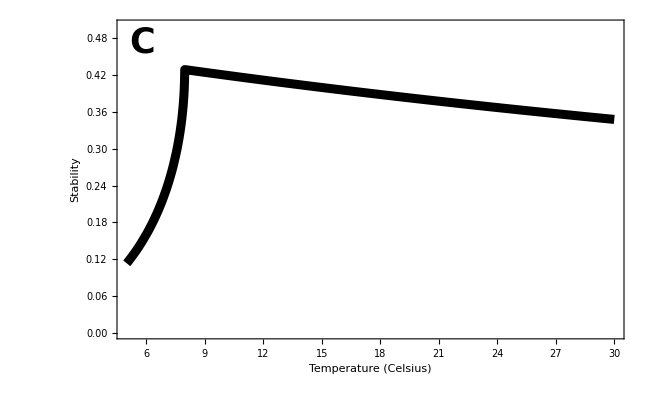

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
PlotRange->{0,0.5},
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos]
}
]

Export[imagedir<>"StabilityAllTempDep.eps",%];
```

With all the dependencies, stability still decreases with temperature, albeit slower than when only K depended on temperature (Gilbert Figure 3c).

The decrease in consumer:resource biomass at high temperatures, relative to Gilbert et al Figure 3B, is largely driven by the temperature dependence of consumer mortality (here we drop that dependence and see consumer:resource biomass increase with temperature, as it did before):

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

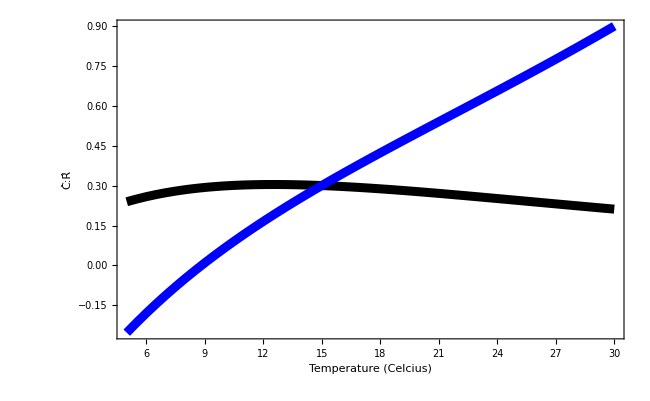

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
Plot[CR[T]/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Blue,Thickness[0.01]},Axes->False],
PlotRange->All,
Frame->True, 
FrameLabel->{Style["Temperature (Celcius)",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None
]
```

The increase in stability at high temperatures, reslative to Gilbert et al Figure 3C, is largely driven by the temperature dependence of consumer mortality (here we drop that dependence and see stability decline, as it did in Gilbert):

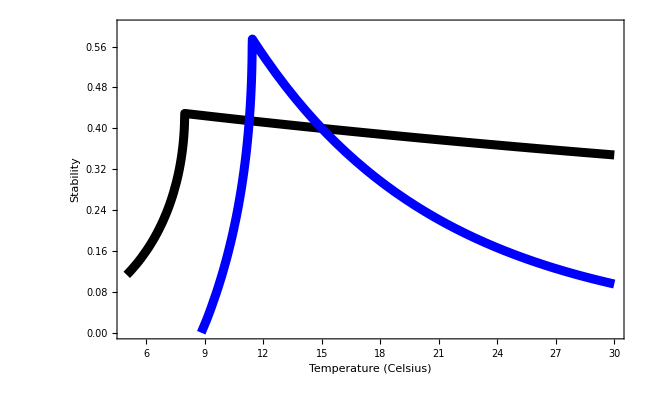

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.aM15/.eM15/.KM15/.rM15/.mM15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0/.Eν[i_]->0.46/.ν0[i_]->1/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Blue,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
PlotRange->{0,0.6},
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None
]
```

## Adding mass-dependence and the temperature-size rule

Now we add dependence on body mass using the relations given in Table 1 of DeLong et al. 2015:

```mathematica
DeLongTable1={
r[M]->r0 M[R]^ρ,
K[M]->K0 M[R]^κ,
a[M]->a0 M[C]^α,
e[M]->e0 M[C]^ϵ,
m[M]->m0 M[C]^μ
};
```

We also want to add the temperature-size rule (TSR). From Forster et al. 2012 Figure 2 this is, for smaller organisms (where the TSR is linear):

```mathematica
TSR=M[i_]->M15[i](1-β[i](T[i]-(273.15+15)));
```

where M15[i], i={R,C}, is the mass of the resource or consumer at 15 degrees Celsius, β[i] is the percent decline in body size with a degree increase in temperature, and T[i] is the current temperature (in Kelvins).

To have the same population dynamics parameter values at 15C as in Gilbert et al 2014 Figure 3 we need

```mathematica
a15=Solve[0.1==a[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,a0]//Flatten
```

{a0→(0.1 M15[C]^(-1. α))/(√(ⅇ^(-(0.00694083 Eν[C])/k) ν0[C]^2+ⅇ^(-(0.00694083 Eν[R])/k) ν0[R]^2))}

```mathematica
e15=Solve[0.15==e[M]/.DeLongTable1/.TSR/.T[i_]->273.15+15,e0]//Flatten
```

{e0→0.15 M15[C]^(-1. ϵ)}

```mathematica
k15=Solve[100==K[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,K0]//Flatten
```

{K0→100. ⅇ^(-(0.00347041 EB)/k+(0.00347041 ES)/k) M15[R]^(-1. κ)}

```mathematica
r15=Solve[2==r[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,r0]//Flatten
```

{r0→2. ⅇ^((0.00347041 EB)/k) M15[R]^(-1. ρ)}

```mathematica
m15=Solve[0.6==m[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,m0]//Flatten
```

{m0→0.6 ⅇ^((0.00347041 Em)/k) M15[C]^(-1. μ)}

Now, BCR as a function of temperature is

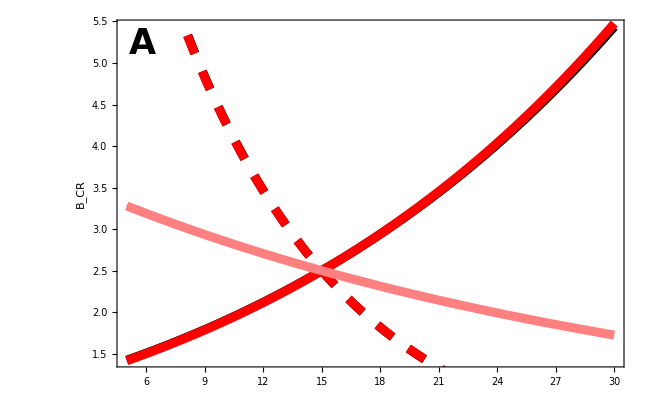

```mathematica
Show[Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thick,Gray}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

Export[imagedir<>"BCRAllTempMassDep.eps",%];
```

As the red curves overlap the black quite closely, the added mass dependence and TSR do not affect the response of BCR to temperature.

Biomass ratios:

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

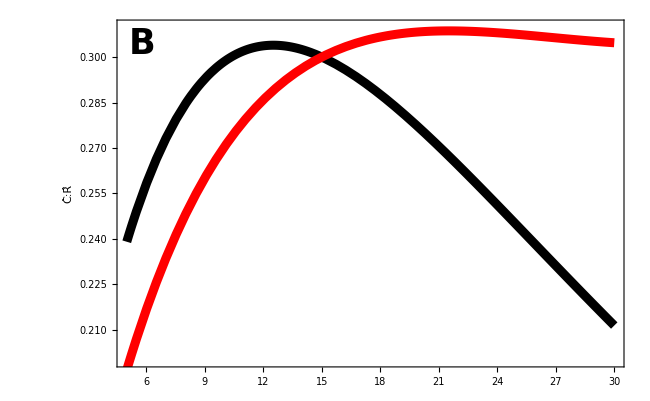

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thickness[0.01]},Axes->False],
PlotRange->{0.2,0.31},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
]

Export[imagedir<>"CtoRAllTempMassDep.eps",%];
```

Here we see that when we add the TSR the ratio no longer decreases over reasonable temperatures. I.e., temperature directly decreases consumer:resource biomass (through its affect on cosumer mortality; see previous section), but it also decreases body sizes, and decreased body size increases consumer:resource biomass (by increasing conversion efficiency and intrinsic growth rate; see below). In other words, the direct and indirect effects of temperature are opposing.

Stability:

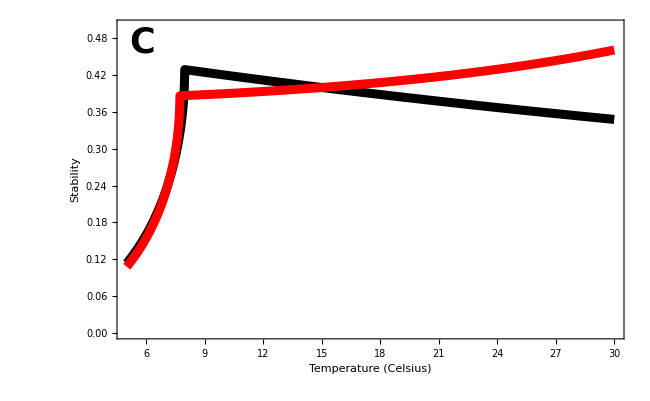

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thickness[0.01]},PlotRange->{0,All}],
PlotRange->{0,0.5},
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos]
}
]

Export[imagedir<>"StabilityAllTempMassDep.eps",%];
```

With the temperature-size rule, stability increases with increasing temperature (as opposed to the decrease without the TSR). Again, temperature directly destabilizes, but indirectly, through its effect on body size (which decreases attack rate and increases intrinsic growth rate), increasing temperature stabilizes the dynamics.

The lack of decrease in C:R at high temperatures, relative to the case without the TSR, is driven by the indirect effect of temperature on conversion efficiency (purple; increases with decreasing body size and hence with temperature) and resource intrinsic growth rate (blue; increases with decreasing body size and hence with temperature. When we drop these effects the curve goes back to the without TSR case:

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

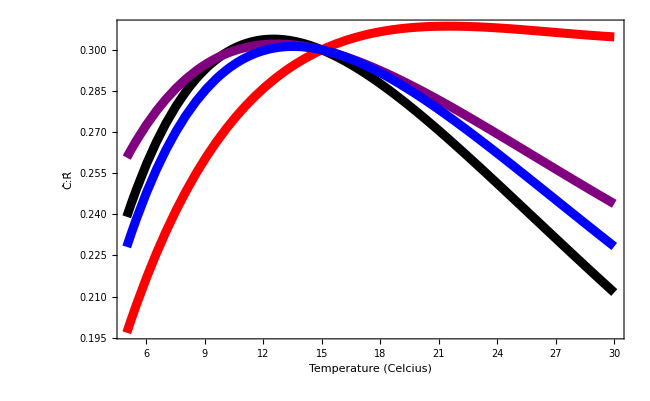

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->0/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Purple,Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->0/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Blue,Thickness[0.01]},Axes->False],
PlotRange->All,
Frame->True, 
FrameLabel->{Style["Temperature (Celcius)",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["",LabelSize,Bold],Scaled@letpos],
Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]
}
]
```

The increase in stability at high temperatures, relative to the case without the TSR, is driven by the indirect effect of temperature on attack rate (which decreases with decreasing body size) and resource intrinsic growth rate (which increases with increasing body size). When we drop these effects the response looks similar to the response without the TSR:

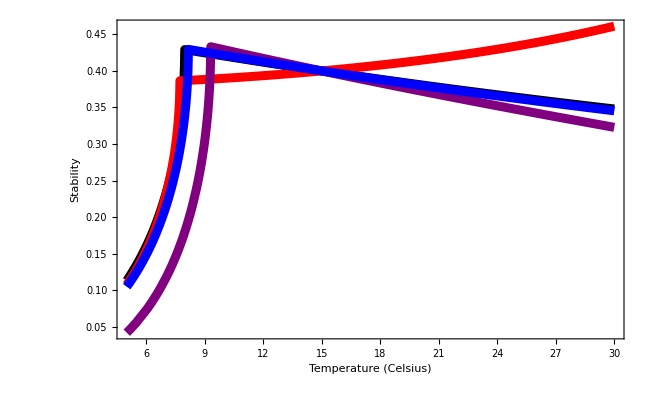

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thickness[0.01]},PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->0/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Purple,Thickness[0.01]},PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->0/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Blue,Thickness[0.01]},PlotRange->{0,All}],
PlotRange->All,
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["",LabelSize,Bold],Scaled@letpos]
}
]
```

## Exploring asymmetric temperature-size responses

In the previous section we’ve supposed that the consumer and resource have the same TSR response. Lets relax that. According to Forster et al 2012, if the consumer is larger than the resource, it might also have a larger TSR response, say maybe a 4% decrease with degree, rather than the 2% for unicells (we are keeping the assumption that the loss is linear).

With a 4% TSR in consumer and a 2% TSR in resource, our predictions become:

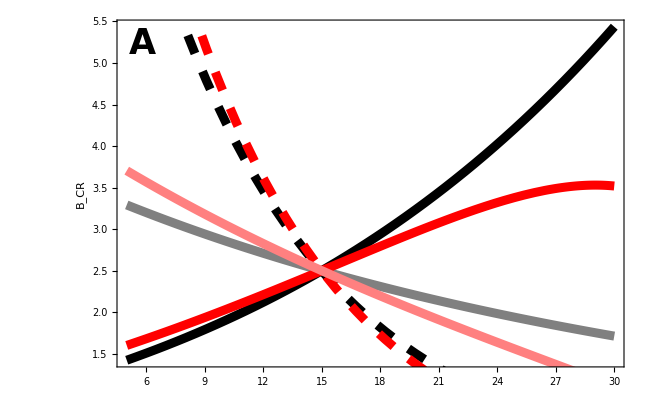

```mathematica
Show[Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Black,Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Gray}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

Export[imagedir<>"BCRAllTempMassDepAsymm.eps",%];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

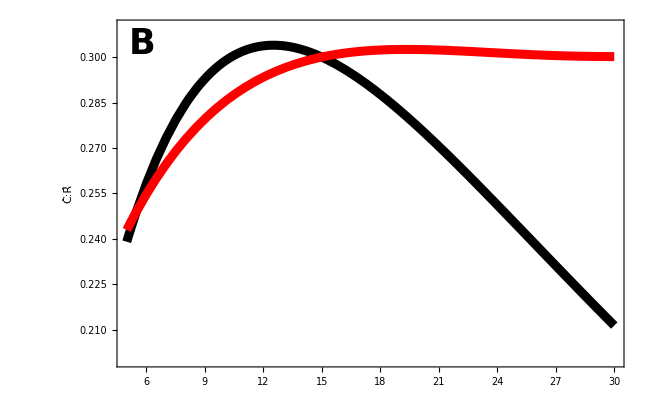

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.04/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thickness[0.01]},Axes->False],
PlotRange->{0.2,0.31},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos]
}
]

Export[imagedir<>"CtoRAllTempMassDepAsymm.eps",%];
```

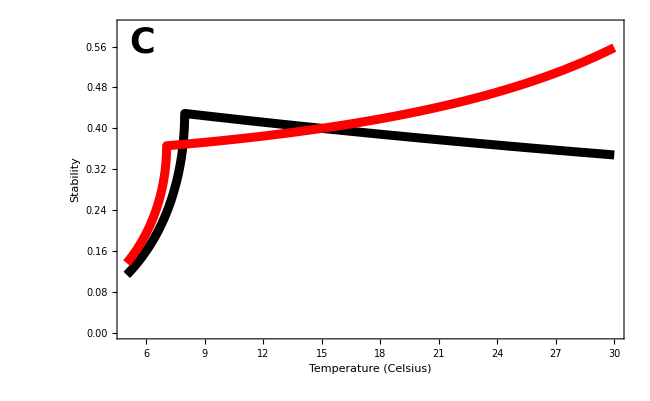

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.03/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thickness[0.01]},PlotRange->{0,All}],
PlotRange->{0,0.6},
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos]
}
]

Export[imagedir<>"StabilityAllTempMassDepAsymm.eps",%];
```

Summary of results:
1. The BCR now changes with the TSR, relative to the case without, albeit only slightly.
2. Not much change in the C:R biomass at equilibrium, relative to the symmetric TSR case.
3. Stability now increases even more with temperature, relative to the symmetric TSR case.

The larger increase in stability is driven by the larger decline in attack rate.

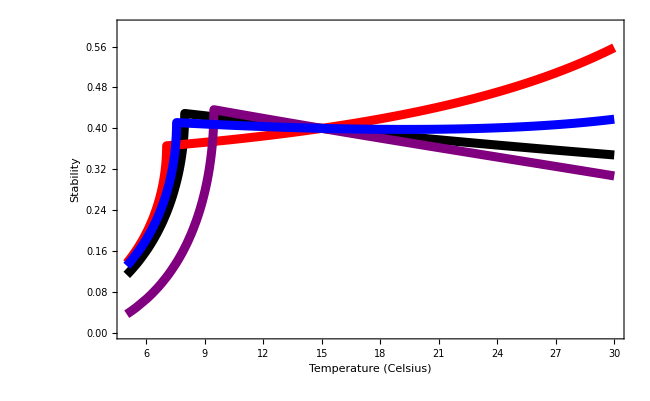

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.03/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thickness[0.01]},PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->0/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[R]->0.02/.β[C]->0.03/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Purple,Thickness[0.01]},PlotRange->{0,All}],
Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->0/.TSR/.β[R]->0.02/.β[C]->0.03/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Blue,Thickness[0.01]},PlotRange->{0,All}],
PlotRange->{0,0.6},
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["",LabelSize,Bold],Scaled@letpos]
}
]
```

## Type-II functional response

BCR at a given T, like that defined by Gilbert et al (Eqn 5), but with type-ll functional response

```mathematica
BCR2[T_]:=(e[T] f[R,T]K[T])/m[C,T] /.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T]
```

Equilibrium biomasses at given temperature assuming a type Il functional response and density-independent consumer mortality

```mathematica
Eq2[T_]:=Solve[{0==dRdt[R,C,T],0==dCdt[R,C,T]}/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],{R,C}]
```

Equilibrium consumer to resource biomass ratio at a given temperature (at the equilibrium where both populations persist)

```mathematica
CR2[T_]:=C/R/.Eq2[T][[3]]
```

The Jacobian evaluated at equilibrium (determines stability)

```mathematica
Jac2={{D[dRdt[R,C,T]/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],R],D[dRdt[R,C,T]/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],C]},{D[dCdt[R,C,T]/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],R],D[dCdt[R,C,T]/.f[R,T]->a[T]/(1+a[T]h[T]R)/.m[C,T]->m[T],C]}}/.Eq2[T][[3]];
```

The eigenvalues of the Jacobian are

```mathematica
lambda2=Eigenvalues[Jac2];
```

Now the dependencies. We can use the scalings of the other parameters from Gilbert and DeLong:

```mathematica
GilbertTable1
```

{r[T]→ⅇ^(-EB/(k T[R])) r[M],K[T]→ⅇ^(EB/(k T[R])-ES/(k T[S])) K[M],m[T]→ⅇ^(-Em/(k T[C])) m[M],a[T]→a[M] √(ⅇ^(-(2 Eν[C])/(k T[C])) ν0[C]^2+ⅇ^(-(2 Eν[R])/(k T[R])) ν0[R]^2),e[T]→e[M]}

```mathematica
DeLongTable1
```

{r[M]→r0 M[R]^ρ,K[M]→K0 M[R]^κ,a[M]→a0 M[C]^α,e[M]→e0 M[C]^ϵ,m[M]→m0 M[C]^μ}

```mathematica
GilbertDeLongT={r[T]->ⅇ^(-EB/(k T[R])) r[M],K[T]->ⅇ^(EB/(k T[R])-ES/(k T[S])) K[M],m[T]->ⅇ^(-Em/(k T[C])) m[M],e[T]->e[M]};
GilbertDeLongM={r[M]->r0 M[R]^ρ,K[M]->K0 M[R]^κ,e[M]->e0 M[C]^ϵ,m[M]->m0 M[C]^μ};
```

The attack rate and handling time scalings are (in a 2D environment; Rall et al. 2012)

```mathematica
RallT={h[T]->ⅇ^(-Eh/(k T[C])) h[M],a[T]->ⅇ^(-Ea/(k T[C])) a[M]};
RallM={h[M]->h0 M[C]^hC M[R]^hR,a[M]->a0 M[C]^aC M[R]^aR};
```

To have the same population dynamics parameter values at 15C as in Gilbert et al. Figure 3, we need

```mathematica
ah15=Solve[0.1==Simplify[a[T]/(1+a[T]h[T]R)/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.T[i_]->273.15+15,a0]//Flatten
```

{a0→(0.1 ⅇ^((0.00347041 Ea)/k) M15[C]^(-1. aC) M15[R]^(-1. aR))/(1.-(1. 1.^(hC-1. ϵ+μ) ⅇ^(-(0.00347041 Eh)/k-(0.00347041 Em)/k) h0 m0 M15[C]^(hC-1. ϵ+μ) M15[R]^hR)/e0)}

```mathematica
e15=Solve[0.15==e[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,e0]//Flatten
```

{e0→0.15 M15[C]^(-1. ϵ)}

```mathematica
k15=Solve[100==K[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,K0]//Flatten
```

{K0→100. ⅇ^(-(0.00347041 EB)/k+(0.00347041 ES)/k) M15[R]^(-1. κ)}

```mathematica
r15=Solve[2==r[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,r0]//Flatten
```

{r0→2. ⅇ^((0.00347041 EB)/k) M15[R]^(-1. ρ)}

```mathematica
m15=Solve[0.6==m[T]/.GilbertTable1/.DeLongTable1/.TSR/.T[i_]->273.15+15,m0]//Flatten
```

{m0→0.6 ⅇ^((0.00347041 Em)/k) M15[C]^(-1. μ)}

Now, BCR as a function of temperature is

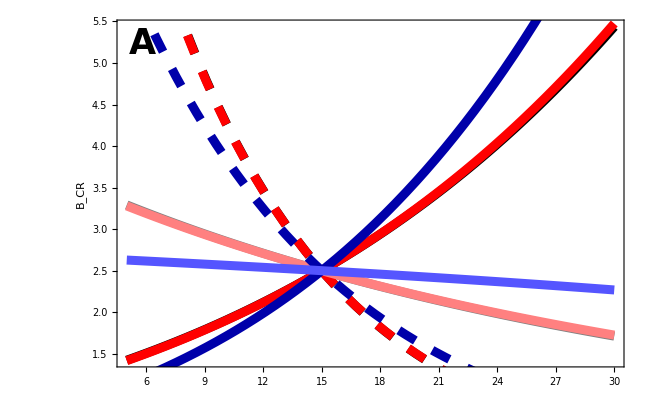

```mathematica
Show[
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Black,Thickness[0.01]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Black,Thickness[0.01],Dashing[Large]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->273.15+t,{t,5,30},PlotStyle->{Gray,Thickness[0.01]}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red}],
Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.32/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Red,Dashing[Large]}],Plot[BCR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.9/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Thickness[0.01],Pink}],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.32/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Darker[Blue],Thickness[0.01]}],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.32/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Darker[Blue],Thickness[0.01],Dashing[Large]}],
Plot[Simplify[BCR2[T]/.Eq2[T][[3]]]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Lighter[Blue],Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["B_CR",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

Export[imagedir<>"BCRTypeII.eps",%];
```

Black is only temperature dependencies and type-1, Red is mass and temperature dependencies with type-1, and Blue is mass and temperature dependencies with type-2.

Biomass ratios:

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

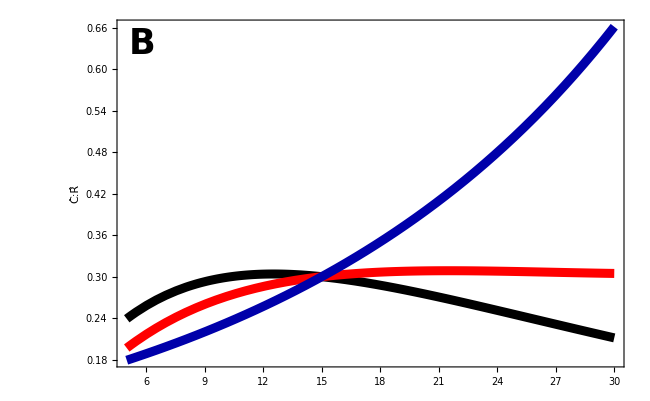

```mathematica
Show[
Plot[CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
Plot[  CR[T]/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15,{T,5,30},PlotStyle->{Red,Thickness[0.01]},Axes->False,PlotRange->{0,All}],
Plot[CR2[T]/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->1/.M15[i_]->1,{t,5,30},PlotStyle->{Darker[Blue],Thickness[0.01]},PlotRange->{0,All}],
PlotRange->{0,All},
Frame->True, 
FrameLabel->{Style[(*"Temperature (Celcius)"*)"",LabelSize],Style["Ĉ:R̂",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos]
}
]

Export[imagedir<>"CtoRTypeII.eps",%];
```

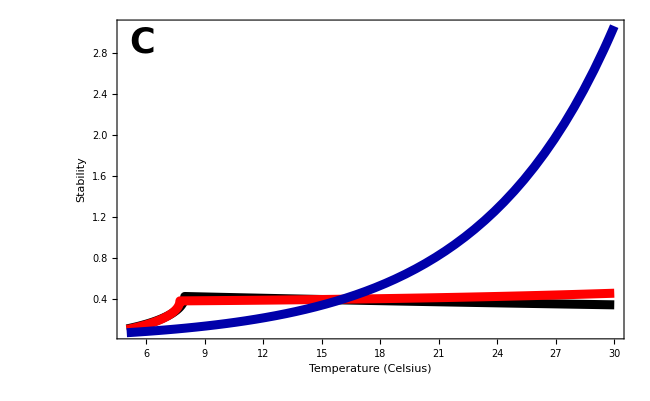

```mathematica
Show[Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Black,Thickness[0.01]},Axes->False,PlotRange->{0,All}],Plot[-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]],{T,5,30},PlotStyle->{Red,Thickness[0.01]},PlotRange->{0,All}],
Plot[-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]],{t,5,30},PlotStyle->{Darker[Blue],Thickness[0.01]},PlotRange->All],
Frame->True, 
FrameLabel->{Style["Temperature (Celsius)",LabelSize],Style["Stability",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
Epilog->{
Text[Style["C",LabelSize,Bold],Scaled@letpos]
},
PlotRange->All
]

Export[imagedir<>"StabilityTypeII.eps",%];
```

Note that although we have to give values for h0 and the M15[i]s in order to produce the blue curves, the results do not depend on them - except in the case of stability, where h0 has a big effect. Setting h0=0 makes stability equal at 15C, but this makes the functional response type-I (the red and blue curves don’t line up anywhere else, despite having the same functional response, because the temperature and mass dependence of attack rate is different in Rall et al. 2012, and stability depends on the derivative of the functional response with respect to R, which is necessarily different with a type-II with h not 0, making them different even at 15C).

The effect of h0 on stability:

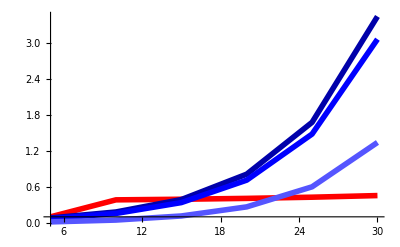

```mathematica
Show[
ListPlot[Table[{T,-Max[Re[lambda/.GilbertTable1/.DeLongTable1/.a15/.e15/.k15/.r15/.m15/.EB->0.32/.ES->0.9/.k->8.62*10^-5/.Em->0.65/.Eν[i_]->0.46/.ν0[i_]->1/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.TSR/.β[i_]->0.02/.T[i_]->T+273.15]]},{T,5,30,5}],PlotStyle->{Red,Thickness[0.01]},PlotRange->All,Joined->True],ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-14/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Darker[Blue],Thickness[0.01]},PlotRange->All, Joined->True],
ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->10^-13/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Blue,Thickness[0.01]},PlotRange->All, Joined->True],
ListPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.h0->5*10^-13/.M15[i_]->1]]},{t,5,30,5}],PlotStyle->{Lighter[Blue],Thickness[0.01]},PlotRange->All, Joined->True],
PlotRange->All
]
```

The increase is exponential (at least when stable):

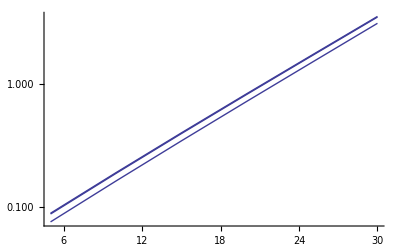

```mathematica
Show[Table[ListLogPlot[Table[{t,-Max[Re[lambda2/.RallT/.RallM/.GilbertDeLongT/.GilbertDeLongM/.TSR/.ah15/.e15/.k15/.r15/.m15/.T[i_]->T/.k->8.62*10^-5/.EB->0.9/.ES->0.9/.Em->0.65/.κ->-0.81/.α->1/.ϵ->-0.5/.μ->-0.29/.ρ->-0.81/.β[i_]->0.02/.T->273.15+t/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.M15[i_]->1/.h0->10^-x]]},
{t,5,30,5}
],
PlotRange->{10^-3,All}, Joined->True
],
{x,10,15,1}],
PlotRange->All
]
```

## Type-II functional response continued: Improving Rall’s fit

Response of capture rate to temperature, with (blue) and without (black) the TSR:

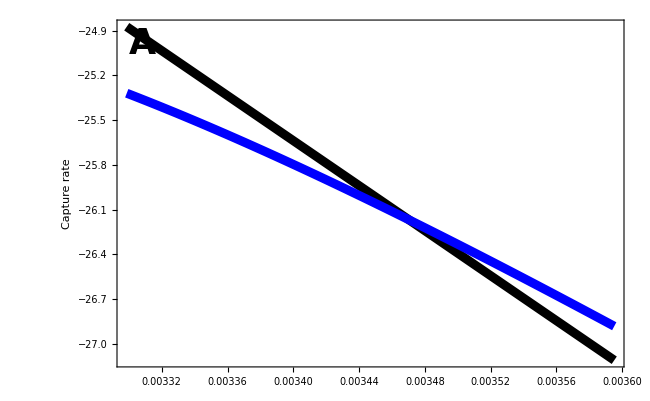

```mathematica
Show[
Plot[Log[a[T]/a0]/.RallT/.RallM/.k->8.62*10^-5/.M[i_]->1/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Black,Thickness[0.01]}],
Plot[Log[a[T]/a0]/.RallT/.RallM/.TSR/.k->8.62*10^-5/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.M15[i_]->1/.β[i_]->0.02/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Blue,Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style[(*"Temperature^-1 (Kelvins^-1)"*)"",LabelSize],Style["Capture rate",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

Export[imagedir<>"CaptureTSRSymm.eps",%];
```

The TSR lowers the activation energy of capture rate, which goes in the same direction as the discrepancy seen in Rall (see Figure 3a in Rall et al 2012).

With an asymmetric TSR this reponse is even stronger			:

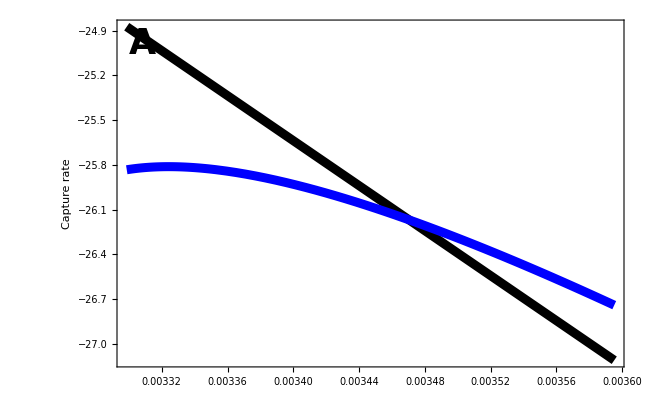

```mathematica
Show[
Plot[Log[a[T]/a0]/.RallT/.RallM/.k->8.62*10^-5/.M[i_]->1/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Black,Thickness[0.01]}],
Plot[Log[a[T]/a0]/.RallT/.RallM/.TSR/.k->8.62*10^-5/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.M15[i_]->1/.β[R]->0.02/.β[C]->0.04/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Blue,Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style[(*"Temperature^-1 (Kelvins^-1)"*)"",LabelSize],Style["Capture rate",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["A",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

Export[imagedir<>"CaptureTSRAsymm.eps",%];
```

And for handling time:

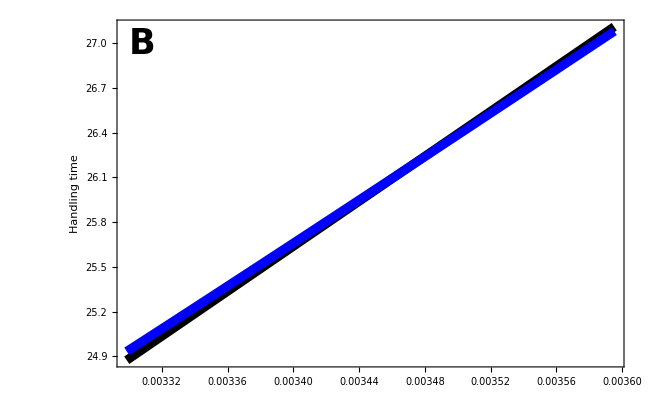

```mathematica
Show[
Plot[Log[h[T]/h0]/.RallT/.RallM/.k->8.62*10^-5/.M[i_]->1/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Black,Thickness[0.01]}],
Plot[Log[h[T]/h0]/.RallT/.RallM/.TSR/.k->8.62*10^-5/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.M15[i_]->1/.β[i_]->0.02/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Blue,Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style[(*"Temperature^-1 (Kelvins^-1)"*)"",LabelSize],Style["Handling time",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

Export[imagedir<>"HandlingTSRSymm.eps",%];
```

Here the TSR (slightly) decreases the activation energy of handling time. But this is with same TSR in resource and consumer. If we allow the consumer to have a larger TSR, then we have

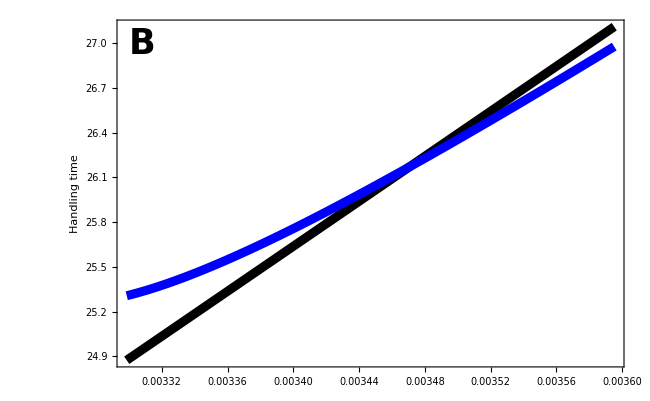

```mathematica
Show[
Plot[Log[h[T]/h0]/.RallT/.RallM/.k->8.62*10^-5/.M[i_]->1/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Black,Thickness[0.01]}],
Plot[Log[h[T]/h0]/.RallT/.RallM/.TSR/.k->8.62*10^-5/.aC->1/4+2/3/.aR->1/3/.hC->-2/3/.hR->0.5/.Ea->0.65/.Eh->-0.65/.M15[R]->1/.M15[C]->1/.β[R]->0.02/.β[C]->0.04/.T[i_]->1/t,{t,1/(273.15+5),1/(273.15+30)},PlotStyle->{Blue,Thickness[0.01]}],
Frame->True, 
FrameLabel->{Style[(*"Temperature^-1 (Kelvins^-1)"*)"",LabelSize],Style["Handling time",LabelSize],,},
FrameStyle->Directive[FontSize->TickSize],
ImagePadding->Pad,
ImageSize->FigureSize,
PlotRangePadding->None,
(*PlotRangeClipping->False,*)
Epilog->{
Text[Style["B",LabelSize,Bold],Scaled@letpos],
(*Rotate[Text[Style["B_CR",LabelSize],Scaled@ylabpos],90 Degree]*)
}
]

Export[imagedir<>"HandlingTSRAsymm.eps",%];
```

which makes the activation energy of handling time smaller, as in Rall (see Figure 3d).

## A functional response that depends on the body size ratio

This section is based on Kalinkat et al. 2013. who discuss how the functional response changes with the ratio of body size between consumer and resources.

In particular, we let the functional response be

```mathematica
g[R_,T_]:=(b[T] R^q[M])/(1+h[T]b[T] R^(1+q[M]))
```

such that when q=0 we have a type-2 functional response and when q>0 we have a type-3 (sigmiodal):

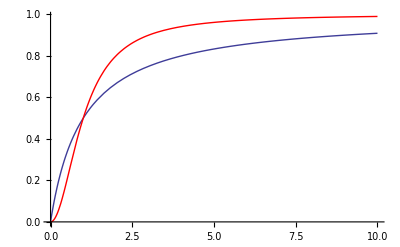

```mathematica
Show[
Plot[g[R,T]R/.b[T]->1/.h[T]->1/.q[M]->0,{R,0,10},PlotRange->{0,All}],
Plot[g[R,T]R/.b[T]->1/.h[T]->1/.q[M]->1,{R,0,10},PlotRange->{0,All},PlotStyle->Red],
PlotRange->{0,All}
]
```

We say q is a function of body  mass M, because it depends on the ratio of consumer to resource body size

```mathematica
q[M_]:=(qmax (M[C]/M[R])^2)/(q0^2+(M[C]/M[R])^2)
```

where qmax and q0 are scaling parameters that determine the shape of the sigmoidal response (qmax is the asymptote, q0^2 is the half-saturation constant):

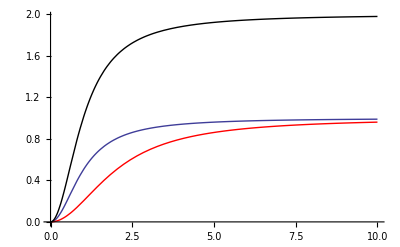

```mathematica
Show[
Plot[q[M]/.M[C]->a M[R]/.qmax->1/.q0->1,{a,0,10},PlotRange->{0,All}],
Plot[q[M]/.M[C]->a M[R]/.qmax->1/.q0->2,{a,0,10},PlotRange->{0,All},PlotStyle->Red],
Plot[q[M]/.M[C]->a M[R]/.qmax->2/.q0->1,{a,0,10},PlotRange->{0,All},PlotStyle->Black]
]
```

The fitted values in Kalinkat give the following curve

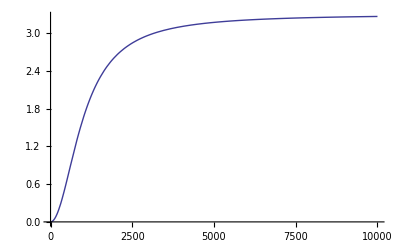

```mathematica
Plot[q[M]/.M[C]->a M[R]/.qmax->3.3/.q0->10^3,{a,0,10^4},PlotRange->{0,All},PlotStyle->Thick]
```

What effect does the TSR have on q?

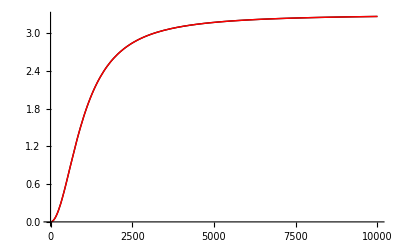

```mathematica
Show[
Plot[q[M]/.qmax->3.3/.q0->10^3/.TSR/.T[i_]->T/.β[R]->0/.β[C]->0/.M15[C]->a M15[R]/.T->273.15+25,{a,0,10^4},PlotRange->{0,All},PlotStyle->Black],
Plot[q[M]/.qmax->3.3/.q0->10^3/.TSR/.T[i_]->T/.β[R]->0.02/.β[C]->0.02/.M15[C]->a M15[R]/.T->273.15+25,{a,0,10^4},PlotRange->{0,All},PlotStyle->Red]
]
```

As we might expect, because q depends on the ratio of body sizes, if both resource and consumer have the same TSR, then the TSR has no affect on q.

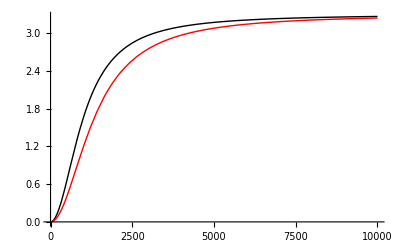

```mathematica
Show[
Plot[q[M]/.qmax->3.3/.q0->10^3/.TSR/.T[i_]->T/.β[R]->0/.β[C]->0/.M15[C]->a M15[R]/.T->273.15+25,{a,0,10^4},PlotRange->{0,All},PlotStyle->Black],
Plot[q[M]/.qmax->3.3/.q0->10^3/.TSR/.T[i_]->T/.β[R]->0.02/.β[C]->0.04/.M15[C]->a M15[R]/.T->273.15+25,{a,0,10^4},PlotRange->{0,All},PlotStyle->Red]
]
```

However, when the consumer has a larger TSR than the resource (4% vs 2%), the body mass ratio decreases with temperature, decreasing q and therefore slowing the switch from type-2 to type-3. Because type-3 is more stable, the TSR may be said to reduce stability by this mechanism (however, as we can see in the above plot, with the TSR (red) q is not reduced by much).